## Выполнение расчетного задания по дисциплине Тепломассообмен в среде Mathematica 14 Студент: Жаркова А.Э. Группа: ТФ-13-22 Задача № 3 -Graphics- Рисунок: цилиндр диаметром d=120mm и высотой L=14 cm -Graphics-

#### Введем исходные данные:

```mathematica
d0=UnitConvert[Quantity[120,"Millimeters"],"Meters"];

r0=d0/2;L=UnitConvert[Quantity[14,"Centimeters"],"Meters"];t0=Quantity[600,"DegreesCelsius"];tLiquid=Quantity[20,"DegreesCelsius"];α=Quantity[130,("Watts")/(("Meters")^2*"Kelvins")];
ρ=Quantity[8666,("Kilograms")/("Meters")^3];
cp=Quantity[343,("Joules")/("Kilograms"*"Kelvins")];
λ=Quantity[26,("Watts")/("Meters"*"Kelvins")];
τ1=UnitConvert[Quantity[1.8,"Minutes"],"Seconds"];
```

#### Найдем коэффициент температуропроводности a:

```mathematica
a=UnitConvert[N[λ/(cp*ρ)],("Meters")^2/("Seconds")]
```

8.74703×10^-6 m^2/s

#### Числа Био по радиальному( BiRadial) и вертикальному( BiVertical) направлениям:

```mathematica
BiRadial=N[(α*r0)/λ]
```

0.3

```mathematica
BiVertical=N[(α*L/2)/λ]
```

0.35

#### Числа Фурье по радиальному( FoRadial) и вертикальному( FoVertical) направлениям:

```mathematica
FoRadial=(a*τ1)/(r0)^2
```

0.262411

```mathematica
FoVertical=(a*τ1)/(L/2)^2
```

0.192792

#### Приступим к поиску корней характеристического уравнения(MATLAB) в радиальном направлении: -Graphics- Отдельно рассмотрим седьмой корень(определим его визуально с точностью е-4) -Graphics-

```mathematica
ϵ={0.7465 ,   3.9091 ,   7.0582  , 10.2029   ,13.3462,   16.4888  , 19.6311};
```

#### В вертикальном направлении: -Graphics- 7 корень: -Graphics-

```mathematica
μ={0.5592    ,3.2489  ,  6.3383   , 9.4618   ,12.5942 ,  15.7302   ,18.8681    };
```

#### Найдем функцию распределения температуры в радиальном направлении:

```mathematica
ΘRadial[r_,τ_]:=Total[(2*BesselJ[1,ϵ])/(ϵ*(BesselJ[0,ϵ]+BesselJ[1,ϵ]^2))*BesselJ[0,ϵ*r/QuantityMagnitude[r0]]*Exp[-ϵ^2*QuantityMagnitude[a]*τ/QuantityMagnitude[r0]^2]];
```

```mathematica
ΘRadial[0,0]
```

1.00904

```mathematica
tRadial[r_,τ_]=tLiquid + (t0-tLiquid)*ΘRadial[r,τ];
```

#### Найдем температуру на оси цилиндра в момент времени τ = 0

```mathematica
tRadial[0,0]
```

878.392 K

```mathematica
UnitConvert[tRadial[0,0],"DegreesCelsius"]
```

605.242 °C

#### Найдем функцию распределения температуры в вертикальном направлении:

```mathematica
ΘVertical[x_,τ_]:=Total[(2*Sin[μ])/(μ+Sin[μ]*Cos[μ])*Cos[μ*x/QuantityMagnitude[L/2]]*Exp[-μ^2*(QuantityMagnitude[a]*τ)/QuantityMagnitude[(L/2)^2]]]
```

```mathematica
ΘVertical[0,0]
```

1.00081

```mathematica
tVertical[x_,τ_]:=tLiquid + (t0-tLiquid)*ΘVertical[x,τ];
```

#### Найдем температуру в центре цилиндра в момент времени τ = 0

```mathematica
tVertical[0,0]
```

873.617 K

```mathematica
UnitConvert[tVertical[0,0],"DegreesCelsius"]
```

600.467 °C

#### Найдем функцию распределения температурного поля в цилиндре t(x,r,τ)

```mathematica
Θ3D[x_,r_,τ_]:=ΘVertical[x,τ]*ΘRadial[r,τ];
```

```mathematica
t[x_,r_,τ_]:=tLiquid + (t0-tLiquid)*Θ3D[x,r,τ];
```

#### Начнем расчет температурного поля Сначала для r=0:

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.07 m | 421.612 °C
0.0525 m | 451.49 °C
0.035 m | 471.128 °C
0.0175 m | 481.842 °C
0. | 485.189 °C)

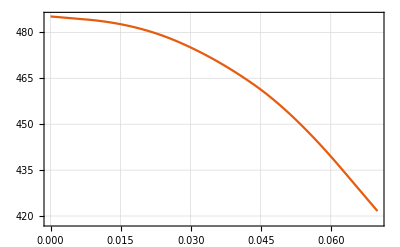

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для r=r0

```mathematica
Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}]//MatrixForm
```

(0.07 m | 367.136 °C
0.0525 m | 392.961 °C
0.035 m | 409.934 °C
0.0175 m | 419.195 °C
0. | 422.088 °C)

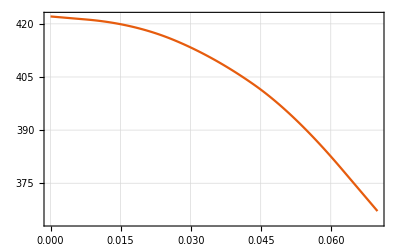

```mathematica
ListLinePlot[Table[{ N[x],UnitConvert[t[QuantityMagnitude[x],QuantityMagnitude[r0],QuantityMagnitude[τ1]],"DegreesCelsius"]},{x,{L/2,3*L/8,L/4,L/8,0}}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=0

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.06 m | 422.088 °C
0.045 m | 448.971 °C
0.03 m | 468.836 °C
0.015 m | 481.059 °C
0. | 485.189 °C)

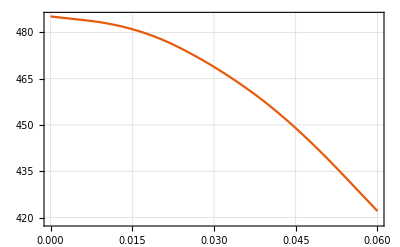

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь для x=L/2

```mathematica
Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}]//MatrixForm
```

(0.06 m | 367.136 °C
0.045 m | 390.344 °C
0.03 m | 407.495 °C
0.015 m | 418.047 °C
0. | 421.612 °C)

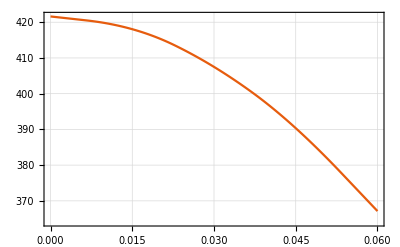

```mathematica
ListLinePlot[Table[{ N[r],UnitConvert[t[QuantityMagnitude[L/2],QuantityMagnitude[r],QuantityMagnitude[τ1]],"DegreesCelsius"]},{r,Reverse[{0,r0/4,r0/2,3*r0/4,r0}]}],InterpolationOrder->2,PlotTheme->"Scientific",GridLines->Automatic]
```

#### Покажем распределение температуры в центре цилиндра и на расстоянии 0.2 d_0 от поверхности как функцию времени Сначала для центра:

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[10]}]//MatrixForm
```

(108. s | 485.189 °C
216. s | 400.83 °C
324. s | 330.078 °C
432. s | 272.256 °C
540. s | 225.192 °C
648. s | 186.906 °C
756. s | 155.763 °C
864. s | 130.431 °C
972. s | 109.826 °C
1080. s | 93.0655 °C)

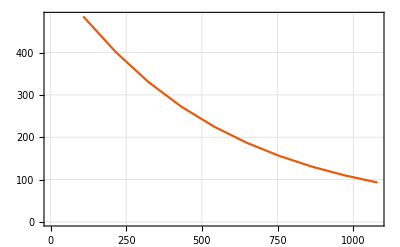

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[10]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Теперь на расстоянии 0.2 d_0 (0.4 r_0)от поверхности , следовательно r=0.6 r_0)

```mathematica
Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[10]}]//MatrixForm
```

(108. s | 461.775 °C
216. s | 381.961 °C
324. s | 314.72 °C
432. s | 259.762 °C
540. s | 215.029 °C
648. s | 178.639 °C
756. s | 149.039 °C
864. s | 124.962 °C
972. s | 105.377 °C
1080. s | 89.4467 °C)

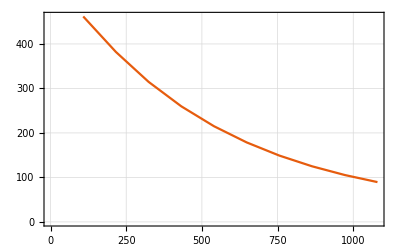

```mathematica
ListLinePlot[Table[{ N[k*τ1],UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]},{k,Range[10]}],PlotTheme->"Scientific",GridLines->Automatic]
```

#### Для определения темпа охлаждения и коэффициента температуропроводности заготовки построит несколько зависимостей ln(θ) используя данные полученные выше( в центре и на 0.6r_0). θ = t-tLiquid

```mathematica
lnForCenter=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[10]}]
```

{{108. s,6.14244},{216. s,5.94235},{324. s,5.73682},{432. s,5.53044},{540. s,5.32395},{648. s,5.11743},{756. s,4.91091},{864. s,4.70439},{972. s,4.49787},{1080. s,4.29136}}

```mathematica
lnForPoint6r0=Table[{ N[k*τ1],Log[QuantityMagnitude[UnitConvert[t[QuantityMagnitude[0],QuantityMagnitude[0.6*r0],QuantityMagnitude[k*τ1]],"DegreesCelsius"]-tLiquid]]},{k,Range[10]}]
```

{{108. s,6.0908},{216. s,5.89154},{324. s,5.68603},{432. s,5.47965},{540. s,5.27315},{648. s,5.06663},{756. s,4.86011},{864. s,4.6536},{972. s,4.44708},{1080. s,4.24056}}

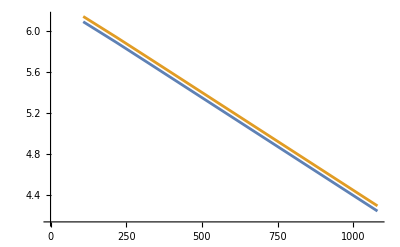

```mathematica
ListLinePlot[{lnForPoint6r0,lnForCenter}]
```

#### Нетрудно заметить,что стадии регулярного режима гарантированно соответствует интервал [400,800] s. Найдем число Фурье в краевых точках интервала регулярного режима и удостоверимся что оно больше 0.3

```mathematica
FoRadialAt400=(a*Quantity[400,"Seconds"])/r0^2
```

0.971892

```mathematica
FoRadialAt800=(a*Quantity[800,"Seconds"])/r0^2
```

1.94378

```mathematica
FoVerticalAt400=(a*Quantity[400,"Seconds"])/(L/2)^2
```

0.714043

```mathematica
FoVerticalAt800=(a*Quantity[800,"Seconds"])/(L/2)^2
```

1.42809

#### Приступим к поиску темпа охлаждения m для наших двух точек

```mathematica
mAtCenter=Log[Θ3D[0,0,400]/Θ3D[0,0,800]]/Quantity[800-400,"Seconds"]
```

0.00191211 per second

```mathematica
mAtPoint6r0=Log[Θ3D[0,QuantityMagnitude[0.6*r0],400]/Θ3D[0,QuantityMagnitude[0.6*r0],800]]/Quantity[800-400,"Seconds"]
```

0.00191211 per second

#### Берем среднее

```mathematica
m=(mAtCenter+mAtPoint6r0)/2
```

0.00191211 per second

#### Fo > 0.3 поэтому ряд Фурье сходится быстро и первый член достаточно описывает все решение. Найдем коэффициент формы K:

```mathematica
K=1/((First[ϵ]/r0)^2+(First[μ]/(L/2))^2)
```

0.00457431 m^2

#### Найдем коэффициент температуропроводности по второй теореме Кондратьева(допущение что наше m=m_∞) и сравним с теоретическим:

```mathematica
aExperimental=K*m
```

4.51927×10^-6 m^2/s

```mathematica
a
```

8.74703×10^-6 m^2/s

```mathematica
δa=Abs[a-aExperimental]/a
```

0.483337

#### Найдем количество теплоты, отданное цилиндром за время τ_1: Для начала найдем сколько теплоты он отдаст до того момента как Θ==0 т.е. t=tLiquid

```mathematica
Q=N[π*(r0)^2*L*ρ*cp*(t0-tLiquid)]
```

2.72974×10^6 J

```mathematica
ΘRadialAverage=Total[(4*BiRadial^2)/(ϵ^2*(ϵ^2+BiRadial^2))*Exp[-ϵ^2*FoRadial]]
```

0.862321

```mathematica
ΘVerticalAverage=Total[(2*Sin[μ]^2)/(μ^2+μ*Sin[μ]*Cos[μ])*Exp[-μ^2*FoVertical]]
```

0.939601

```mathematica
ΘAverage=ΘVerticalAverage*ΘRadialAverage
```

0.810238

```mathematica
Qτ1=Q(1-ΘAverage)
```

518002. J

#### Подытожим полным температурным полем в момент времени τ_1

```mathematica
data=Flatten[Table[{x,r,t[QuantityMagnitude[x],QuantityMagnitude[r],QuantityMagnitude[τ1]]},{x,0,L/2,L/4},{r,0,r0,r0/4}],1];

ListPlot3D[data,Boxed->True,Mesh->None,PlotStyle->Directive[Opacity[0.7],Yellow],AxesLabel->{"x (m)","r (m)","t (°C)"},LabelStyle->Directive[Medium,Black],InterpolationOrder->4]
```

-Graphics3D-